```mathematica
FinancialData["NASDAQ:AAPL","Price"]
```

202.64 $

```mathematica
aapl=FinancialData["NASDAQ:AAPL","Price",All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
aapl=FinancialData["NASDAQ:AAPL","Price",All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
aapl=FinancialData["NASDAQ:AAPL","Price",All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
aapl=FinancialData["NASDAQ:AAPL","Price",All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
aapl
```

$Failed

```mathematica
ClearAll[aapl]
```

```mathematica
FinancialData["NASDAQ:AAPL","Price"]
```

202.64 $

```mathematica
FinancialData["NASDAQ:AAPL","Price",All]
```

TimeSeries[…]

```mathematica
Options[Out[9]]
```

{}

```mathematica
Out[9]["Dates"][[;;10]]
```

{Fri 12 Dec 1980 00:00:00GMT-7.,Mon 15 Dec 1980 00:00:00GMT-7.,Tue 16 Dec 1980 00:00:00GMT-7.,Wed 17 Dec 1980 00:00:00GMT-7.,Thu 18 Dec 1980 00:00:00GMT-7.,Fri 19 Dec 1980 00:00:00GMT-7.,Mon 22 Dec 1980 00:00:00GMT-7.,Tue 23 Dec 1980 00:00:00GMT-7.,Wed 24 Dec 1980 00:00:00GMT-7.,Fri 26 Dec 1980 00:00:00GMT-7.}

```mathematica
Transpose[{Out[9]["Dates"][[;;-1]],Out[9]["Values"]}]
```

{{Fri 12 Dec 1980 00:00:00GMT-7.,0.51 $},{Mon 15 Dec 1980 00:00:00GMT-7.,0.49 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.45 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.46 $},{Thu 18 Dec 1980 00:00:00GMT-7.,0.48 $},{Fri 19 Dec 1980 00:00:00GMT-7.,0.50 $},{Mon 22 Dec 1980 00:00:00GMT-7.,0.53 $},{Tue 23 Dec 1980 00:00:00GMT-7.,0.55 $},{Wed 24 Dec 1980 00:00:00GMT-7.,0.58 $},{Fri 26 Dec 1980 00:00:00GMT-7.,0.63 $},9746,{Tue 13 Aug 2019 00:00:00GMT-7.,208.97 $},{Wed 14 Aug 2019 00:00:00GMT-7.,202.75 $},{Thu 15 Aug 2019 00:00:00GMT-7.,201.74 $},{Fri 16 Aug 2019 00:00:00GMT-7.,206.50 $},{Mon 19 Aug 2019 00:00:00GMT-7.,210.35 $},{Tue 20 Aug 2019 00:00:00GMT-7.,210.36 $},{Wed 21 Aug 2019 00:00:00GMT-7.,212.64 $},{Thu 22 Aug 2019 00:00:00GMT-7.,212.46 $},{Fri 23 Aug 2019 00:00:00GMT-7.,202.64 $}}
 |  |  |  |

```mathematica
TakeLargestBy[Transpose[{Out[9]["Dates"][[;;-1]],Out[9]["Values"]}],Last,10]
```

{{Wed 3 Oct 2018 00:00:00GMT-7.,232.07 $},{Tue 2 Oct 2018 00:00:00GMT-7.,229.28 $},{Tue 4 Sep 2018 00:00:00GMT-7.,228.36 $},{Thu 4 Oct 2018 00:00:00GMT-7.,227.99 $},{Fri 31 Aug 2018 00:00:00GMT-7.,227.63 $},{Mon 1 Oct 2018 00:00:00GMT-7.,227.26 $},{Wed 5 Sep 2018 00:00:00GMT-7.,226.87 $},{Tue 9 Oct 2018 00:00:00GMT-7.,226.87 $},{Thu 13 Sep 2018 00:00:00GMT-7.,226.41 $},{Fri 28 Sep 2018 00:00:00GMT-7.,225.74 $}}

```mathematica
Grid@TakeLargestBy[Transpose[{Out[9]["Dates"][[;;-1]],Out[9]["Values"]}],Last,10]
```

Wed 3 Oct 2018 00:00:00GMT-7. | 232.07 $
Tue 2 Oct 2018 00:00:00GMT-7. | 229.28 $
Tue 4 Sep 2018 00:00:00GMT-7. | 228.36 $
Thu 4 Oct 2018 00:00:00GMT-7. | 227.99 $
Fri 31 Aug 2018 00:00:00GMT-7. | 227.63 $
Mon 1 Oct 2018 00:00:00GMT-7. | 227.26 $
Wed 5 Sep 2018 00:00:00GMT-7. | 226.87 $
Tue 9 Oct 2018 00:00:00GMT-7. | 226.87 $
Thu 13 Sep 2018 00:00:00GMT-7. | 226.41 $
Fri 28 Sep 2018 00:00:00GMT-7. | 225.74 $

```mathematica
With[{ts=FinancialData["NASDAQ:MSFT","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
Out[9]["Dates"][[;;-1]],
Out[9]["Values"]}]
,Last,10]
]
```

Wed 3 Oct 2018 00:00:00GMT-7. | 232.07 $
Tue 2 Oct 2018 00:00:00GMT-7. | 229.28 $
Tue 4 Sep 2018 00:00:00GMT-7. | 228.36 $
Thu 4 Oct 2018 00:00:00GMT-7. | 227.99 $
Fri 31 Aug 2018 00:00:00GMT-7. | 227.63 $
Mon 1 Oct 2018 00:00:00GMT-7. | 227.26 $
Wed 5 Sep 2018 00:00:00GMT-7. | 226.87 $
Tue 9 Oct 2018 00:00:00GMT-7. | 226.87 $
Thu 13 Sep 2018 00:00:00GMT-7. | 226.41 $
Fri 28 Sep 2018 00:00:00GMT-7. | 225.74 $

```mathematica
With[{ts=FinancialData["NASDAQ:GOOG","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
Out[9]["Dates"][[;;-1]],
Out[9]["Values"]}]
,Last,10]
]
```

Wed 3 Oct 2018 00:00:00GMT-7. | 232.07 $
Tue 2 Oct 2018 00:00:00GMT-7. | 229.28 $
Tue 4 Sep 2018 00:00:00GMT-7. | 228.36 $
Thu 4 Oct 2018 00:00:00GMT-7. | 227.99 $
Fri 31 Aug 2018 00:00:00GMT-7. | 227.63 $
Mon 1 Oct 2018 00:00:00GMT-7. | 227.26 $
Wed 5 Sep 2018 00:00:00GMT-7. | 226.87 $
Tue 9 Oct 2018 00:00:00GMT-7. | 226.87 $
Thu 13 Sep 2018 00:00:00GMT-7. | 226.41 $
Fri 28 Sep 2018 00:00:00GMT-7. | 225.74 $

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
Out[9]["Dates"][[;;-1]],
Out[9]["Values"]}]
,Last,10]
]
```

Wed 3 Oct 2018 00:00:00GMT-7. | 232.07 $
Tue 2 Oct 2018 00:00:00GMT-7. | 229.28 $
Tue 4 Sep 2018 00:00:00GMT-7. | 228.36 $
Thu 4 Oct 2018 00:00:00GMT-7. | 227.99 $
Fri 31 Aug 2018 00:00:00GMT-7. | 227.63 $
Mon 1 Oct 2018 00:00:00GMT-7. | 227.26 $
Wed 5 Sep 2018 00:00:00GMT-7. | 226.87 $
Tue 9 Oct 2018 00:00:00GMT-7. | 226.87 $
Thu 13 Sep 2018 00:00:00GMT-7. | 226.41 $
Fri 28 Sep 2018 00:00:00GMT-7. | 225.74 $

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-1]],
ts["Values"]}]
,Last,10]
]
```

Wed 25 Jul 2018 00:00:00GMT-7. | 217.50 $
Tue 24 Jul 2018 00:00:00GMT-7. | 214.67 $
Mon 23 Jul 2018 00:00:00GMT-7. | 210.91 $
Tue 17 Jul 2018 00:00:00GMT-7. | 209.99 $
Fri 20 Jul 2018 00:00:00GMT-7. | 209.94 $
Wed 18 Jul 2018 00:00:00GMT-7. | 209.36 $
Thu 19 Jul 2018 00:00:00GMT-7. | 208.09 $
Fri 13 Jul 2018 00:00:00GMT-7. | 207.32 $
Mon 16 Jul 2018 00:00:00GMT-7. | 207.23 $
Thu 12 Jul 2018 00:00:00GMT-7. | 206.92 $

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-1]],
ts["Values"]}]
,Last,10]
]
```

Wed 3 Oct 2018 00:00:00GMT-7. | 232.07 $
Tue 2 Oct 2018 00:00:00GMT-7. | 229.28 $
Tue 4 Sep 2018 00:00:00GMT-7. | 228.36 $
Thu 4 Oct 2018 00:00:00GMT-7. | 227.99 $
Fri 31 Aug 2018 00:00:00GMT-7. | 227.63 $
Mon 1 Oct 2018 00:00:00GMT-7. | 227.26 $
Wed 5 Sep 2018 00:00:00GMT-7. | 226.87 $
Tue 9 Oct 2018 00:00:00GMT-7. | 226.87 $
Thu 13 Sep 2018 00:00:00GMT-7. | 226.41 $
Fri 28 Sep 2018 00:00:00GMT-7. | 225.74 $

```mathematica
With[{ts=FinancialData["NASDAQ:GOOG","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-1]],
ts["Values"]}]
,Last,10]
]
```

Mon 29 Apr 2019 00:00:00GMT-7. | 1 287.58 $
Fri 26 Apr 2019 00:00:00GMT-7. | 1 272.18 $
Thu 26 Jul 2018 00:00:00GMT-7. | 1 268.33 $
Tue 23 Apr 2019 00:00:00GMT-7. | 1 264.55 $
Wed 25 Jul 2018 00:00:00GMT-7. | 1 263.70 $
Thu 25 Apr 2019 00:00:00GMT-7. | 1 263.45 $
Wed 24 Apr 2019 00:00:00GMT-7. | 1 256.00 $
Fri 26 Jul 2019 00:00:00GMT-7. | 1 250.41 $
Wed 29 Aug 2018 00:00:00GMT-7. | 1 249.30 $
Thu 9 Aug 2018 00:00:00GMT-7. | 1 249.10 $

```mathematica
With[{ts=FinancialData["NASDAQ:MSFT","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-1]],
ts["Values"]}]
,Last,10]
]
```

Fri 26 Jul 2019 00:00:00GMT-7. | 141.34 $
Mon 29 Jul 2019 00:00:00GMT-7. | 141.03 $
Wed 24 Jul 2019 00:00:00GMT-7. | 140.72 $
Tue 30 Jul 2019 00:00:00GMT-7. | 140.35 $
Thu 25 Jul 2019 00:00:00GMT-7. | 140.19 $
Tue 23 Jul 2019 00:00:00GMT-7. | 139.29 $
Mon 15 Jul 2019 00:00:00GMT-7. | 138.90 $
Fri 12 Jul 2019 00:00:00GMT-7. | 138.90 $
Thu 8 Aug 2019 00:00:00GMT-7. | 138.89 $
Wed 21 Aug 2019 00:00:00GMT-7. | 138.79 $

```mathematica
With[{ts=FinancialData["NASDAQ:AMZN","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-1]],
ts["Values"]}]
,Last,10]
]
```

Tue 4 Sep 2018 00:00:00GMT-7. | 2 039.51 $
Mon 15 Jul 2019 00:00:00GMT-7. | 2 020.99 $
Wed 10 Jul 2019 00:00:00GMT-7. | 2 017.41 $
Thu 27 Sep 2018 00:00:00GMT-7. | 2 012.98 $
Fri 31 Aug 2018 00:00:00GMT-7. | 2 012.71 $
Fri 12 Jul 2019 00:00:00GMT-7. | 2 011.00 $
Tue 16 Jul 2019 00:00:00GMT-7. | 2 009.90 $
Mon 1 Oct 2018 00:00:00GMT-7. | 2 004.36 $
Fri 28 Sep 2018 00:00:00GMT-7. | 2 003.00 $
Thu 30 Aug 2018 00:00:00GMT-7. | 2 002.38 $

```mathematica
With[{ts=FinancialData["NASDAQ:AMZN","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-1]],
ts["Values"]}]
,Last,10]
]
```

Thu 22 May 1997 00:00:00GMT-7. | 1.40 $
Wed 4 Jun 1997 00:00:00GMT-7. | 1.42 $
Wed 21 May 1997 00:00:00GMT-7. | 1.43 $
Tue 3 Jun 1997 00:00:00GMT-7. | 1.48 $
Fri 27 Jun 1997 00:00:00GMT-7. | 1.49 $
Mon 23 Jun 1997 00:00:00GMT-7. | 1.50 $
Fri 30 May 1997 00:00:00GMT-7. | 1.50 $
Fri 23 May 1997 00:00:00GMT-7. | 1.50 $
Tue 17 Jun 1997 00:00:00GMT-7. | 1.51 $
Thu 29 May 1997 00:00:00GMT-7. | 1.51 $

```mathematica
With[{ts=FinancialData["NASDAQ:AMZN","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-1]],
Differences@ts["Values"]}]
,Last,10]
]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

TakeSmallestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeSmallestBy[Transpose[{{Thu 15 May 1997 00:00:00GMT-7.,Fri 16 May 1997 00:00:00GMT-7.,Mon 19 May 1997 00:00:00GMT-7.,Tue 20 May 1997 00:00:00GMT-7.,Wed 21 May 1997 00:00:00GMT-7.,Thu 22 May 1997 00:00:00GMT-7.,5595,Fri 16 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Tue 20 Aug 2019 00:00:00GMT-7.,Wed 21 Aug 2019 00:00:00GMT-7.,Thu 22 Aug 2019 00:00:00GMT-7.,Fri 23 Aug 2019 00:00:00GMT-7.},{-0.23 $,-0.02 $,-0.07 $,-0.21 $,-0.03 $,5597,-14.74 $,22.16 $,-17.94 $,-55.98 $}}],Last,10]]
 |  |  |  |

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-1]],
Differences@ts["Values"]}]
,Last,10]
]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

TakeSmallestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeSmallestBy[Transpose[{{Fri 18 May 2012 00:00:00GMT-7.,Mon 21 May 2012 00:00:00GMT-7.,Tue 22 May 2012 00:00:00GMT-7.,Wed 23 May 2012 00:00:00GMT-7.,Thu 24 May 2012 00:00:00GMT-7.,Fri 25 May 2012 00:00:00GMT-7.,1811,Fri 16 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Tue 20 Aug 2019 00:00:00GMT-7.,Wed 21 Aug 2019 00:00:00GMT-7.,Thu 22 Aug 2019 00:00:00GMT-7.,Fri 23 Aug 2019 00:00:00GMT-7.},{-4.20 $,-3.03 $,1.00 $,1.03 $,-1.12 $,1812,2.47 $,-2.36 $,-0.26 $,-1.51 $,-4.29 $}}],Last,10]]
 |  |  |  |

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-1]],
Differences@ts["Values"]
}]
,Last,10]
]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

TakeSmallestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeSmallestBy[Transpose[{{Fri 18 May 2012 00:00:00GMT-7.,Mon 21 May 2012 00:00:00GMT-7.,Tue 22 May 2012 00:00:00GMT-7.,Wed 23 May 2012 00:00:00GMT-7.,Thu 24 May 2012 00:00:00GMT-7.,Fri 25 May 2012 00:00:00GMT-7.,1811,Fri 16 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Tue 20 Aug 2019 00:00:00GMT-7.,Wed 21 Aug 2019 00:00:00GMT-7.,Thu 22 Aug 2019 00:00:00GMT-7.,Fri 23 Aug 2019 00:00:00GMT-7.},{-4.20 $,-3.03 $,1.00 $,1.03 $,-1.12 $,1812,2.47 $,-2.36 $,-0.26 $,-1.51 $,-4.29 $}}],Last,10]]
 |  |  |  |

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"],
Differences@ts["Values"]
}]
,Last,10]
]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

TakeSmallestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeSmallestBy[Transpose[{{Fri 18 May 2012 00:00:00GMT-7.,Mon 21 May 2012 00:00:00GMT-7.,Tue 22 May 2012 00:00:00GMT-7.,Wed 23 May 2012 00:00:00GMT-7.,Thu 24 May 2012 00:00:00GMT-7.,Fri 25 May 2012 00:00:00GMT-7.,1811,Fri 16 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Tue 20 Aug 2019 00:00:00GMT-7.,Wed 21 Aug 2019 00:00:00GMT-7.,Thu 22 Aug 2019 00:00:00GMT-7.,Fri 23 Aug 2019 00:00:00GMT-7.},{-4.20 $,-3.03 $,1.00 $,1.03 $,-1.12 $,1812,2.47 $,-2.36 $,-0.26 $,-1.51 $,-4.29 $}}],Last,10]]
 |  |  |  |

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Transpose[{
ts["Dates"],
Differences@ts["Values"]
}]
]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose[{{Fri 18 May 2012 00:00:00GMT-7.,Mon 21 May 2012 00:00:00GMT-7.,Tue 22 May 2012 00:00:00GMT-7.,Wed 23 May 2012 00:00:00GMT-7.,Thu 24 May 2012 00:00:00GMT-7.,Fri 25 May 2012 00:00:00GMT-7.,Tue 29 May 2012 00:00:00GMT-7.,1810,Fri 16 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Tue 20 Aug 2019 00:00:00GMT-7.,Wed 21 Aug 2019 00:00:00GMT-7.,Thu 22 Aug 2019 00:00:00GMT-7.,Fri 23 Aug 2019 00:00:00GMT-7.},{-4.20 $,-3.03 $,1.00 $,1816,-0.26 $,-1.51 $,-4.29 $}}]
 |  |  |  |

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Transpose[{
ts["Dates"][[;;-1]],
Differences@ts["Values"]
}]
]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose[{{Fri 18 May 2012 00:00:00GMT-7.,Mon 21 May 2012 00:00:00GMT-7.,Tue 22 May 2012 00:00:00GMT-7.,Wed 23 May 2012 00:00:00GMT-7.,Thu 24 May 2012 00:00:00GMT-7.,Fri 25 May 2012 00:00:00GMT-7.,Tue 29 May 2012 00:00:00GMT-7.,1810,Fri 16 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Tue 20 Aug 2019 00:00:00GMT-7.,Wed 21 Aug 2019 00:00:00GMT-7.,Thu 22 Aug 2019 00:00:00GMT-7.,Fri 23 Aug 2019 00:00:00GMT-7.},{-4.20 $,-3.03 $,1.00 $,1816,-0.26 $,-1.51 $,-4.29 $}}]
 |  |  |  |

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
{Length@ts["Dates"],
Length@Differences@ts["Values"]}
]
```

{1823,1822}

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Last,10]
]
```

Wed 25 Jul 2018 00:00:00GMT-7. | -41.24 $
Fri 31 May 2019 00:00:00GMT-7. | -13.32 $
Fri 16 Mar 2018 00:00:00GMT-7. | -12.53 $
Tue 18 Dec 2018 00:00:00GMT-7. | -10.42 $
Fri 2 Feb 2018 00:00:00GMT-7. | -9.02 $
Tue 13 Aug 2019 00:00:00GMT-7. | -8.74 $
Wed 7 Feb 2018 00:00:00GMT-7. | -8.60 $
Thu 20 Dec 2018 00:00:00GMT-7. | -8.45 $
Thu 11 Jan 2018 00:00:00GMT-7. | -8.40 $
Tue 23 Oct 2018 00:00:00GMT-7. | -8.35 $

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Last,10]
]
```

Wed 30 Jan 2019 00:00:00GMT-7. | 16.27 $
Wed 27 Jan 2016 00:00:00GMT-7. | 14.66 $
Wed 25 Apr 2018 00:00:00GMT-7. | 14.47 $
Wed 24 Apr 2019 00:00:00GMT-7. | 10.68 $
Mon 24 Dec 2018 00:00:00GMT-7. | 10.12 $
Fri 3 Aug 2018 00:00:00GMT-7. | 7.91 $
Wed 24 Jul 2013 00:00:00GMT-7. | 7.85 $
Wed 27 Apr 2016 00:00:00GMT-7. | 7.84 $
Fri 14 Jun 2019 00:00:00GMT-7. | 7.68 $
Wed 29 Jan 2014 00:00:00GMT-7. | 7.55 $

```mathematica
With[{ts=FinancialData["NASDAQ:MFSF","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Last,10]
]
```

Fri 9 Dec 2016 00:00:00GMT-7. | 2.30 $
Wed 1 Feb 2017 00:00:00GMT-7. | 2.20 $
Wed 26 Jun 2019 00:00:00GMT-7. | 2.05 $
Mon 27 Oct 2003 00:00:00GMT-7. | 1.85 $
Thu 9 Feb 2017 00:00:00GMT-7. | 1.80 $
Thu 21 Jun 2018 00:00:00GMT-7. | 1.70 $
Thu 1 Jun 2017 00:00:00GMT-7. | 1.70 $
Tue 30 Sep 2003 00:00:00GMT-7. | 1.50 $
Wed 7 Dec 2016 00:00:00GMT-7. | 1.45 $
Thu 14 Dec 2017 00:00:00GMT-7. | 1.45 $

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Last,10]
]
```

Tue 31 Jul 2018 00:00:00GMT-7. | 11.21 $
Tue 29 Jan 2019 00:00:00GMT-7. | 10.57 $
Mon 24 Dec 2018 00:00:00GMT-7. | 10.34 $
Tue 30 Apr 2019 00:00:00GMT-7. | 9.85 $
Mon 12 Aug 2019 00:00:00GMT-7. | 8.49 $
Fri 23 Mar 2018 00:00:00GMT-7. | 7.83 $
Thu 11 Oct 2018 00:00:00GMT-7. | 7.66 $
Tue 1 May 2018 00:00:00GMT-7. | 7.47 $
Tue 31 Jan 2017 00:00:00GMT-7. | 7.40 $
Tue 24 Apr 2012 00:00:00GMT-7. | 7.10 $

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
Grid@
TakeLargestBy[
Transpose[{
ts["Dates"][[;;-2]],
Ratios@ts["Values"]
}]
,Last,10]
]
```

Tue 5 Aug 1997 00:00:00GMT-7. | 1.33214
Wed 31 Dec 1997 00:00:00GMT-7. | 1.23781
Wed 17 Jul 1996 00:00:00GMT-7. | 1.23702
Mon 5 Jan 1998 00:00:00GMT-7. | 1.19284
Thu 14 Oct 1993 00:00:00GMT-7. | 1.18948
Tue 20 Oct 1987 00:00:00GMT-7. | 1.17392
Thu 10 Jul 1997 00:00:00GMT-7. | 1.14609
Thu 8 Oct 1998 00:00:00GMT-7. | 1.13983
Fri 10 Oct 2008 00:00:00GMT-7. | 1.13905
Thu 2 Aug 1984 00:00:00GMT-7. | 1.13469

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-2]],
Ratios@ts["Values"]
}]
,Last,10]
]
```

Thu 28 Sep 2000 00:00:00GMT-7. | 0.481309
Thu 22 Sep 1983 00:00:00GMT-7. | 0.746165
Fri 16 Oct 1987 00:00:00GMT-7. | 0.756478
Thu 15 Jul 1993 00:00:00GMT-7. | 0.769227
Fri 23 Oct 1987 00:00:00GMT-7. | 0.788731
Fri 26 Sep 2008 00:00:00GMT-7. | 0.820802
Fri 3 Jan 1997 00:00:00GMT-7. | 0.821809
Tue 17 Jul 2001 00:00:00GMT-7. | 0.828286
Tue 5 Dec 2000 00:00:00GMT-7. | 0.841908
Tue 18 Jun 2002 00:00:00GMT-7. | 0.849627

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
Grid@
TakeSmallestBy[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Last,10]
]
```

Wed 2 Jan 2019 00:00:00GMT-7. | -15.73 $
Thu 1 Nov 2018 00:00:00GMT-7. | -14.74 $
Fri 10 May 2019 00:00:00GMT-7. | -11.46 $
Fri 2 Aug 2019 00:00:00GMT-7. | -10.68 $
Tue 9 Oct 2018 00:00:00GMT-7. | -10.51 $
Fri 9 Nov 2018 00:00:00GMT-7. | -10.30 $
Thu 22 Aug 2019 00:00:00GMT-7. | -9.82 $
Wed 23 Jan 2013 00:00:00GMT-7. | -9.07 $
Mon 19 Nov 2018 00:00:00GMT-7. | -8.88 $
Mon 3 Dec 2018 00:00:00GMT-7. | -8.13 $

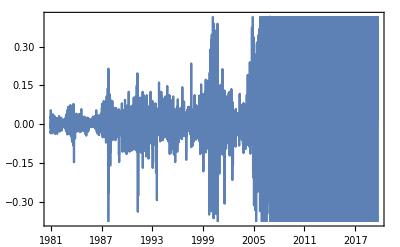

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]]
]
```

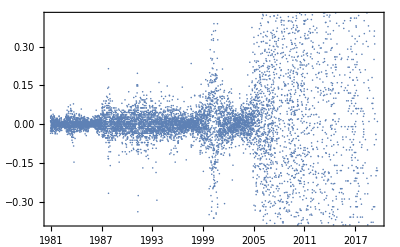

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Joined->False]
]
```

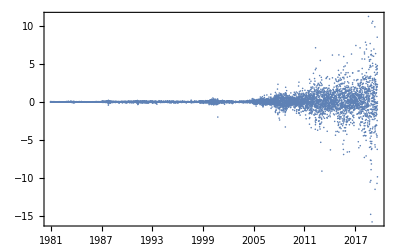

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Joined->False,PlotRange->Full]
]
```

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Joined->False,PlotRange->Full,ImageSize->Full]
]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
Histogram[
Differences@ts["Values"]
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
]
```

-Graphics-

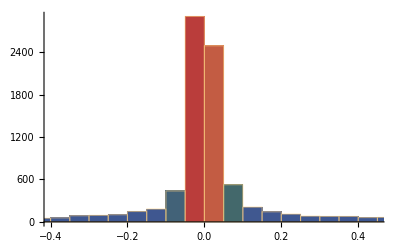
{-Graphics-,-Graphics-}

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
With[{diff=Differences@ts["Values"]},
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
With[{diff=Differences@ts["Values"]},
Grid@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

Grid[{-Graphics-,-Graphics-}]

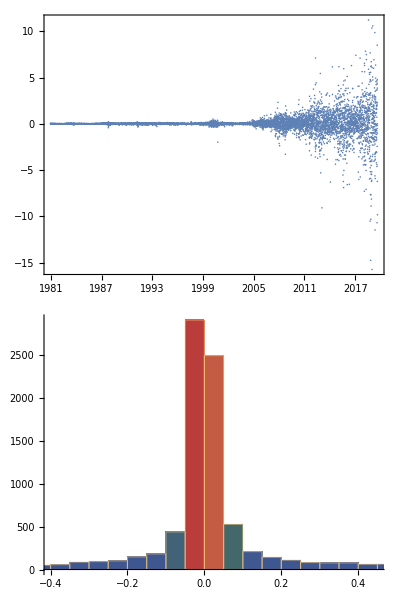

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

```mathematica
With[{ts=FinancialData["NASDAQ:AAPL","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:FB","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:MFSF","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:AMZN","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:GOOG","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

-Graphics-

```mathematica
With[{ts=FinancialData["NASDAQ:GOOGL","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

DateListPlot::ldata: Transpose[{$Failed[],Differences[$Failed[Values]]}] is not a valid dataset or list of datasets.

Histogram::ldata: Differences[$Failed[Values]] is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

DateListPlot[Transpose[{$Failed[],Differences[$Failed[Values]]}],Joined→False,PlotRange→Full,ImageSize→Full,ColorFunction→DarkRainbow]
Histogram[Differences[$Failed[Values]],PlotRange→Full,ImageSize→Full,ColorFunction→DarkRainbow]

```mathematica
With[{ts=FinancialData["NASDAQ:GOOGL","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

DateListPlot::ldata: Transpose[{$Failed[],Differences[$Failed[Values]]}] is not a valid dataset or list of datasets.

Histogram::ldata: Differences[$Failed[Values]] is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

DateListPlot[Transpose[{$Failed[],Differences[$Failed[Values]]}],Joined→False,PlotRange→Full,ImageSize→Full,ColorFunction→DarkRainbow]
Histogram[Differences[$Failed[Values]],PlotRange→Full,ImageSize→Full,ColorFunction→DarkRainbow]

```mathematica
With[{ts=FinancialData["NASDAQ:TSLA","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

DateListPlot::ldata: Transpose[{$Failed[],Differences[$Failed[Values]]}] is not a valid dataset or list of datasets.

Histogram::ldata: Differences[$Failed[Values]] is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

DateListPlot[Transpose[{$Failed[],Differences[$Failed[Values]]}],Joined→False,PlotRange→Full,ImageSize→Full,ColorFunction→DarkRainbow]
Histogram[Differences[$Failed[Values]],PlotRange→Full,ImageSize→Full,ColorFunction→DarkRainbow]

```mathematica
With[{ts=FinancialData["NYSE:IBM","Price",All]},
With[{diff=Differences@ts["Values"]},
Column@
{DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
diff
}]
,Joined->False,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"],
Histogram[
diff
,PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow"]
}
]]
```

-Graphics-